```mathematica
Get[NotebookDirectory[]<>#]&/@
{"combine_packages.wls",
"load_Kramer_data.wl"
};
```

```mathematica
(*transform to Show instead of Two-axis*)
```

```mathematica
figureNameShortTermFinalState1D="final_state_1D_short_term";
figureDirectoryShortTermFinalState1D=figureNameShortTermFinalState1D;
```

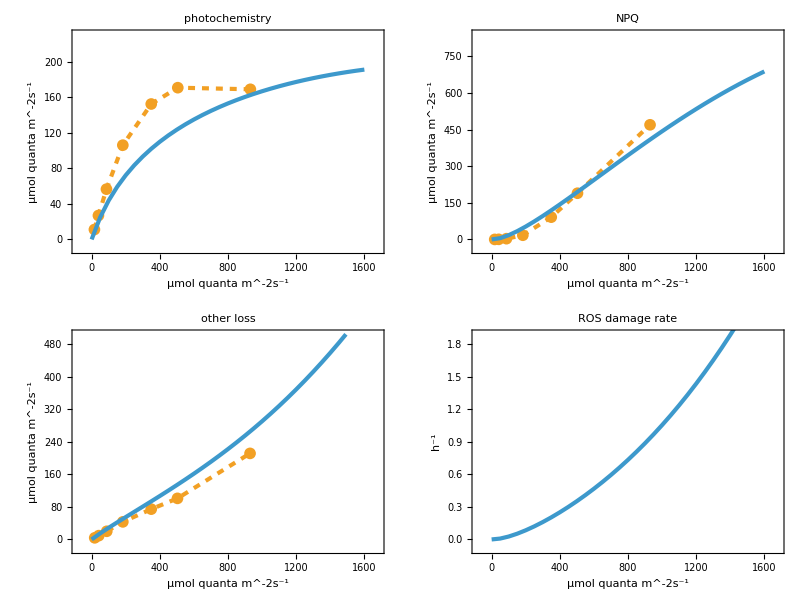

```mathematica
LrangeFates=Range[0,1600,50];
LFateRanges={gP->220,gN->800,gU->480,xD->3600  5 10^-4};
KramerDataPlots=Table[ListPlot[
x/.{gP->gKramer[[1]],gN->gKramer[[2]],gU->gKramer[[3]],xD->{{}}},
PlotRange->{{-.05(Max[LrangeFates]-Min[LrangeFates]),1.05Max[LrangeFates]},{-.05,1.05}(x/.LFateRanges)},PlotLabel->(x/.namesVerbal),imageSizePadding[ImagePaddingUnits],
PlotStyle->{thickness, Dashed,colorPoints},
AxesOrigin->Automatic,
PlotMarkers->plotMarkers,
FrameLabel->{{If[TrueQ[x==xD],"h^-1",L/.units],None},{L/.units,None}},Joined->True,PlotStyle->{AbsoluteThickness[3],Dashed},Evaluate@style],{x,{gP,gN,gU,xD}}];
finalTimeFatePlot=1/60 3600;
LightFateSimulations=Table[makeOneSimulationSteadyStatePlot[pars[-6](*Join[parsNoDamage,pars[-6]]*),L,LrangeFates,{x}, finalTimeFatePlot,{PlotRange->{{-.05(Max[LrangeFates]-Min[LrangeFates]),1.05Max[LrangeFates]},{-.05,1.05}(x/.LFateRanges)},PlotStyle->{{thickness, colorCurves}}}],{x,{gP,gN,gU,3600 xD}}];

(Export[NotebookDirectory[]<>"export/fates-of-light-data-vs-simulations-overlayed.pdf",#];#)&@Multicolumn[Table[Show[{KramerDataPlots[[i]],LightFateSimulations[[i]]}],{i,4}], Appearance -> "Horizontal"]
```

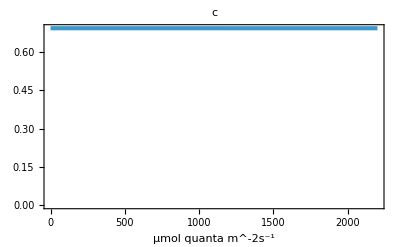
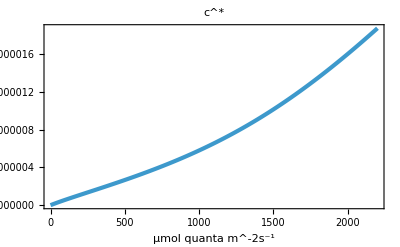
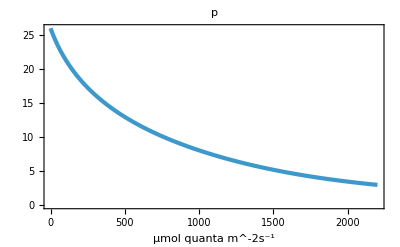
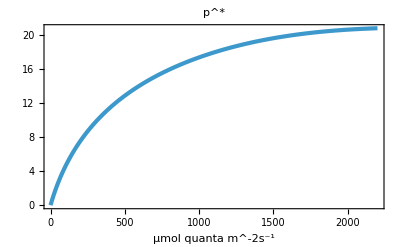
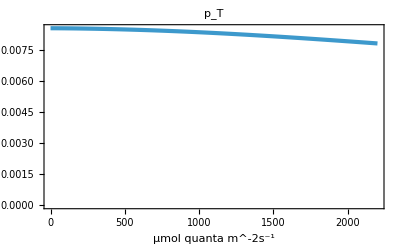
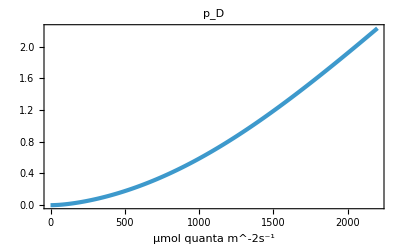
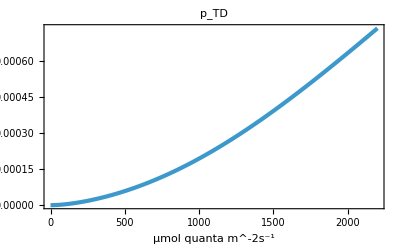
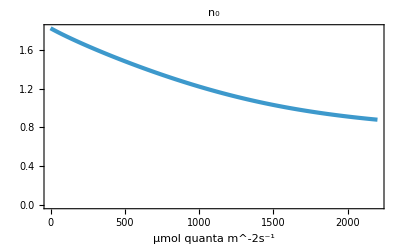

```mathematica
(Export[NotebookDirectory[]<>"export/"<>figureDirectoryShortTermFinalState1D<>"/"<>figureNameShortTermFinalState1D<>"-light.pdf",#];#)&@GridMap[makeOneSimulationSteadyStatePlot[pars[-6],L,Lrange,{#},finalTimeFatePlot,{PlotLabel->#/.names}]&,quants]
```